### Parameters

```mathematica
nn=501;
ll=50;
prec=500;
nData=2000;
γ=0.5//N[#,prec]&;
J=1//N[#,prec]&;
λ=0.5//N[#,prec]&;
a0=λ//N[#,prec]&;
a1=J(1-γ)/2//N[#,prec]&;
a2=J (1+γ)/2//N[#,prec]&;
```

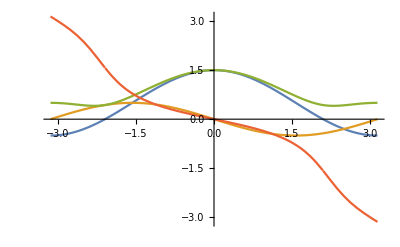

```mathematica
α[θ_]=(a0+(a2+a1) Cos[θ]);
β[θ_]=(a1-a2) Sin[θ];
ω[θ_]=Sqrt[α[θ]^2+β[θ]^2];
ϕ[θ_]=ArcTan[α[θ],β[θ]];
Plot[{α[x],β[x],ω[x],ϕ[x]},{x,-π,π}]
```

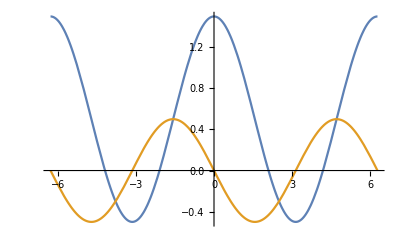

```mathematica
Plot[{α[x],β[x]},{x,-2π,2π}]
```

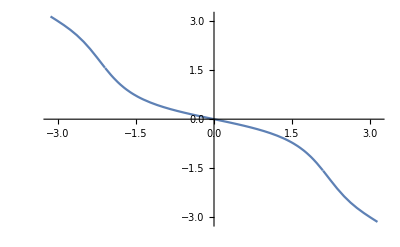

```mathematica
Plot[{ϕ[x]},{x,-π,π}]
```

```mathematica
Series[ArcTan[Sin[x]/(a+Cos[x])],{x,0,7}]
```

x/(1+a)+((a-a^2) x^3)/(6 (1+a)^3)+1/5 (-(2-a)/(2 (1+a)^4)+(1/(1+a)^4-2/(3 (1+a)^3)+a/(3 (1+a)^3))/(1+a)+5 (-1/(12 (1+a)^2)+1/(120 (1+a))+(1/(4 (1+a)^2)-1/(24 (1+a)))/(1+a))) x^5+1/7 (((2-a) (1/(1+a)^4-2/(3 (1+a)^3)+a/(3 (1+a)^3)))/(2 (1+a)^2)+(-1/(1+a)^6+4/(3 (1+a)^5)-(2 a)/(3 (1+a)^5)-11/(18 (1+a)^4)+a/(9 (1+a)^4)-a^2/(36 (1+a)^4)+1/(4 (1+a)^3)-1/(60 (1+a)^2))/(1+a)-(5 (-1/(12 (1+a)^2)+1/(120 (1+a))+(1/(4 (1+a)^2)-1/(24 (1+a)))/(1+a)))/(1+a)^2+7 (1/(240 (1+a)^2)-1/(5040 (1+a))-(1/(4 (1+a)^2)-1/(24 (1+a)))/(6 (1+a))+(1/(8 (1+a)^3)-1/(24 (1+a)^2)+1/(720 (1+a)))/(1+a))) x^7+O[x]^8

### Fourier Transform

```mathematica
t=Table[k,{k,-(nn-1)/2,(nn-1)/2}];
(*mCos=Table[RandomInteger[{0,1}]-1/2,{k,1,(nn-1)/2}];
mCos0=RandomInteger[{0,1}]-1/2;
mSin=Table[RandomInteger[{0,1}]-1/2,{k,1,(nn-1)/2}];
mSin0=RandomInteger[{0,1}]-1/2;*)
```

```mathematica
(*MPlusBand=((If[#==0,(mCos0+mSin0)/2,(mCos⟦Abs[#]⟧+mSin⟦Abs[#]⟧)/2]) E^(I Sign[(2 π)/nn #] ϕ[Abs[(2 π)/nn #]])&/@t)//RotateLeft[#,(nn-1)/2]&//Fourier//Chop;
MMinusAntiBand=((If[#==0,(mCos0-mSin0)/2,(mCos⟦Abs[#]⟧-mSin⟦Abs[#]⟧)/2]) E^(I Sign[(2 π)/nn #] ϕ[Abs[(2 π)/nn #]])&/@t)//RotateLeft[#,(nn-1)/2]&//Fourier//Chop;*)
```

```mathematica
(*MPlus=Table[RotateRight[Take[MPlusBand,ll],j-1],{j,ll}];
MMinus=Table[RotateLeft[Take[MMinusAntiBand,ll],j-1],{j,ll}];*)
```

```mathematica
Now
μ=2//N[#,prec]&;
βT=1/100//N[#,prec]&;
p[l_]=1/(Exp[βT (ω[((2 π)/nn) l]-μ)]+1);
rand=Table[RandomReal[π],{k,1,(nn-1)/2}];
Data=Table[
mCos=Table[If[RandomReal[]>p[k],-(1/2),1/2],{k,1,(nn-1)/2}];
mCos0=If[RandomReal[]>p[0],-(1/2),1/2];
mSin=Table[If[RandomReal[]>p[k],-(1/2),1/2],{k,1,(nn-1)/2}];
mSin0=If[RandomReal[]>p[0],-(1/2),1/2];
MPlusBand=((If[#==0,(mCos0+mSin0)/2,(mCos⟦Abs[#]⟧+mSin⟦Abs[#]⟧)/2]) E^(I Sign[(2 π)/nn #] ϕ[Abs[(2 π)/nn #]])&/@t)//RotateLeft[#,(nn-1)/2]&//Fourier;
MMinusAntiBand=((If[#==0,(mCos0-mSin0)/2,(mCos⟦Abs[#]⟧-mSin⟦Abs[#]⟧)/2]) E^(I Sign[(2 π)/nn #] (ϕ[Abs[(2 π)/nn #]]+2 rand⟦Abs[#]⟧))&/@t)//RotateLeft[#,(nn-1)/2]&//Fourier;
(*MEspRed=
Table[RotateRight[Take[MPlusBand,ll],j-1],{j,ll}]
+Table[RotateLeft[Take[MMinusAntiBand,ll],j-1],{j,ll}];
Flatten[MEspRed]-Mean[Flatten[MEspRed]],*)
Join[Take[MPlusBand,ll],Take[MMinusAntiBand,ll]],
{ii,nData}];
Now
```

Tue 14 Aug 2018 10:11:27

Tue 14 Aug 2018 10:13:29

```mathematica
Now
DataCentered=Table[Data⟦k⟧-(Mean[Data]),{k,1,nData}];
Now
```

Tue 14 Aug 2018 10:13:29

Tue 14 Aug 2018 10:13:33

### Spatial Modes

```mathematica
SpatialModes=Table[
bab=Partition[DataCentered⟦i⟧//Re,ll];
SingularValueDecomposition[Table[RotateRight[bab⟦1⟧,j-1],{j,1,ll}]+Table[RotateLeft[bab⟦2⟧,j-1],{j,1,ll}]],
{i,1,nData}];
```

```mathematica
Table[{ListLinePlot[SpatialModes⟦i,1,1⟧],ListLinePlot[SpatialModes⟦i,3,1⟧]},{i,1,5}];
```

### PCA Covariance Matrix

```mathematica
Cov=1/nData Sum[TensorProduct[DataCentered⟦i⟧,DataCentered⟦i⟧],{i,nData}]//Timing;
Cov⟦1⟧
```

0.668

```mathematica
EigenCov=Eigensystem[Cov⟦2⟧]//Timing;
EigenCov⟦1⟧
```

0.232

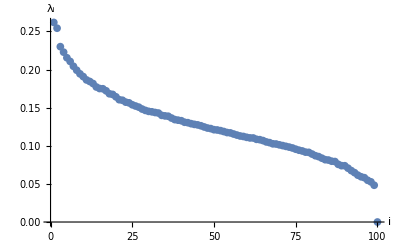

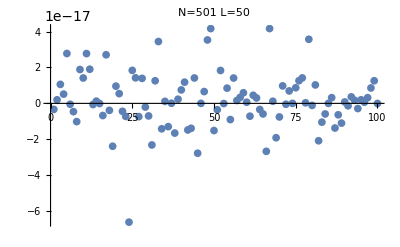

```mathematica
ListPlot[EigenCov⟦2,1⟧//Re//Take[#,;;]&,PlotRange->All,AxesLabel-> {"i","λ_i"}]
ListPlot[EigenCov⟦2,1⟧//Im//Take[#,;;]&,PlotRange->All,PlotLabel-> "N=501  L=50"]
```

#### Plots

{-Graphics3D-,-Graphics3D-}

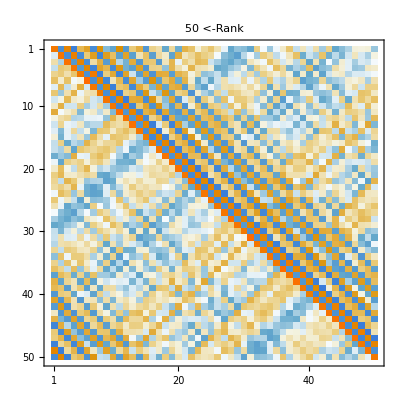
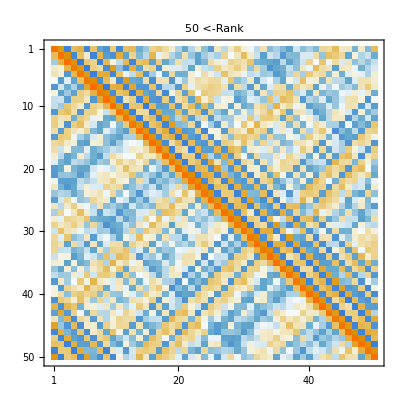

```mathematica
nPCA=20;
BAB=Table[Partition[EigenCov⟦2,2,i⟧//Re,ll],{i,nPCA}];
M=Table[Table[RotateRight[BAB⟦i,1⟧,j-1],{j,1,ll}]+Table[RotateLeft[BAB⟦i,2⟧,j-1],{j,1,ll}],{i,nPCA}];
Plots3D=Table[ListPlot3D[M⟦i⟧,PlotRange->All(*,PlotLabel->"<-Rank"MatrixRank[M⟦i⟧]*)],{i,2}]
PlotsMatrices=Table[MatrixPlot[M⟦i⟧,PlotRange->All,PlotLabel->"<-Rank"MatrixRank[M⟦i⟧]],{i,2}]
```

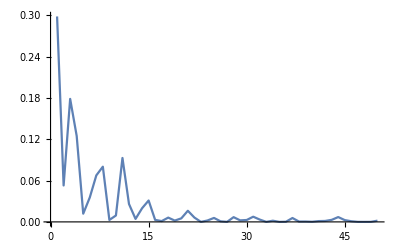
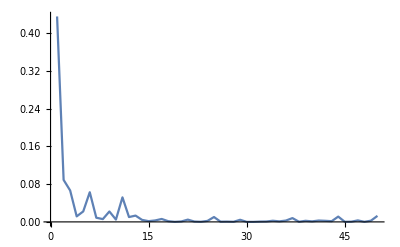

```mathematica
Table[ListLinePlot[M⟦i,1⟧^2,PlotRange->All],{i,1,2}]
```

```mathematica
Plots3D⟦1⟧
Plots3D⟦2⟧
ListLinePlot[M⟦1,1⟧^2,PlotRange->All]
ListLinePlot[M⟦2,1⟧^2//Abs,PlotRange->All]
(*
ListLinePlot[Diagonal[Reverse/@M⟦1⟧],PlotRange->All];
Table[ListLinePlot[Diagonal[Reverse/@M⟦1⟧,i]^2,PlotRange->All],{i,0,10}];
Plots3D⟦3⟧;
Plots3D⟦4⟧;
Plots3D⟦5⟧;
Plots3D⟦6⟧;
*)
```

-Graphics3D-

-Graphics3D-

-Graphics-

-Graphics-

#### Comparison with Barouch & McCoy

```mathematica
c1=γ (1-λ^2/(1-γ^2))^(1/2);
c2=λ/(1-γ^2);
ξ=((-2 √(2c1)ⅇ^(-βT c1))/(π √(βT (1-γ^2))c2)(Gamma[1/2]+(3/(4c1)+(2 c1)/((1-γ^2) c2^2) ) Gamma[3/2] βT^-1+(5/(2(1-γ^2)c2^2)-5/(32 c1^2(1-γ^2)^2 c2^4)) Gamma[5/2] βT^-2))^-1
```

1.82116×10^-7

```mathematica
BigOs=SingularValueDecomposition[Chop[Table[RotateRight[Take[Mean[Data],ll],j-1],{j,1,ll}]+Table[RotateLeft[Take[Mean[Data],-ll],j-1],{j,1,ll}]]];
ρ=1/2 ((BigOs⟦1⟧)^2+ (BigOs⟦3⟧)^2);
```

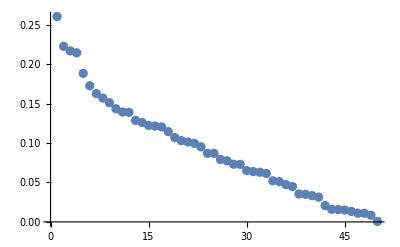

```mathematica
BigOs⟦2⟧//Diagonal //ListPlot
```

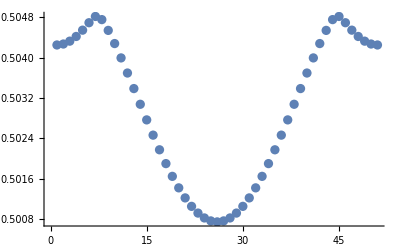

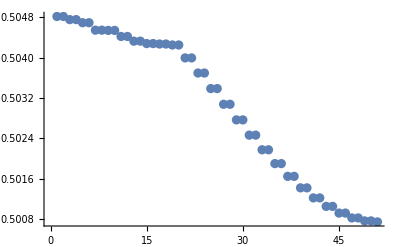

```mathematica
ωs= ω /@ Table[2π q/ll,{q,-ll/2,ll/2}];
ωs //ListPlot;
mω = Max[ωs];
ns = 1/(ⅇ^(βT (# -μ))+1)&/@ωs;
ns//ListPlot[#,PlotRange->All]&
ns//Sort//Reverse//ListPlot[#,PlotRange->All]&
```

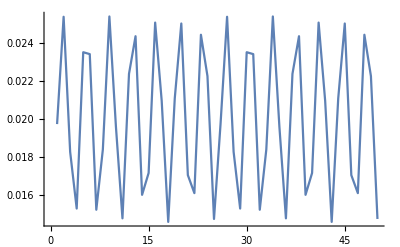
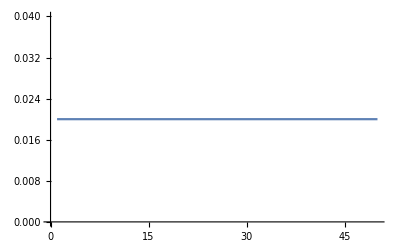
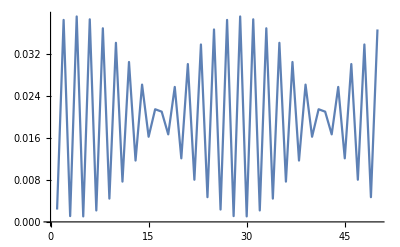
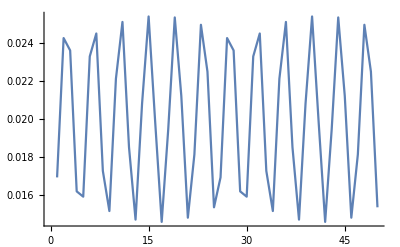
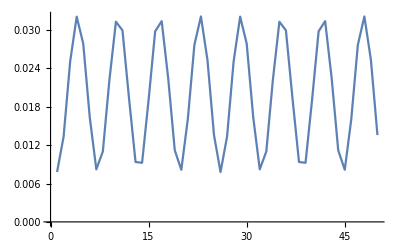
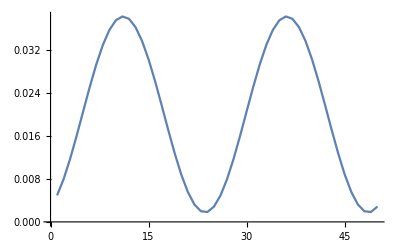
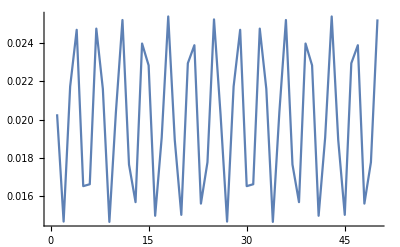
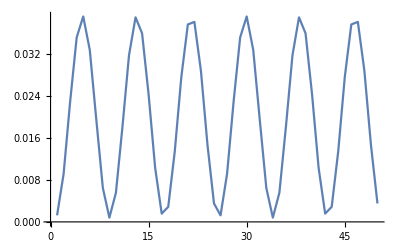
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

-Graphics3D-

```mathematica
ParticipationPlotsAll=ListLinePlot[Table[ρ⟦All,i⟧,{i,1,ll}],ImageSize->Large,PlotRange->All];
Table[ListLinePlot[ρ⟦All,i⟧//Re,PlotRange->All],{i,1,ll}]
ListPlot3D[ρ,PlotRange->All,ImageSize->Large]
```

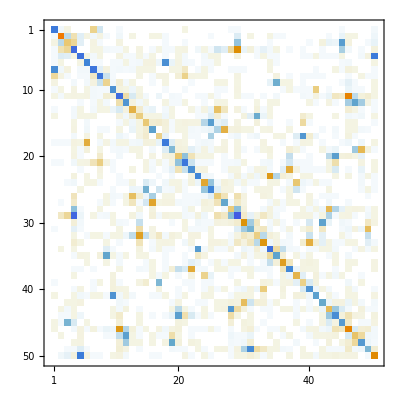
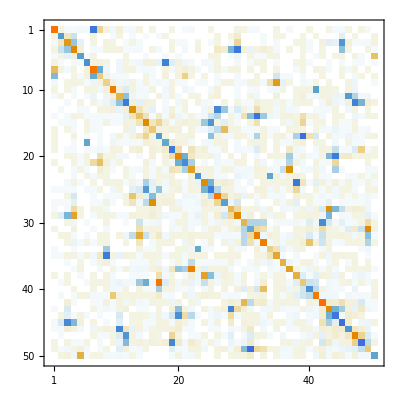
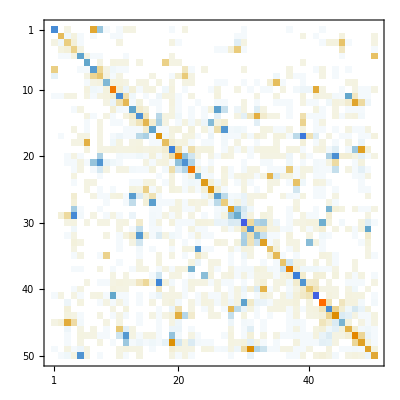
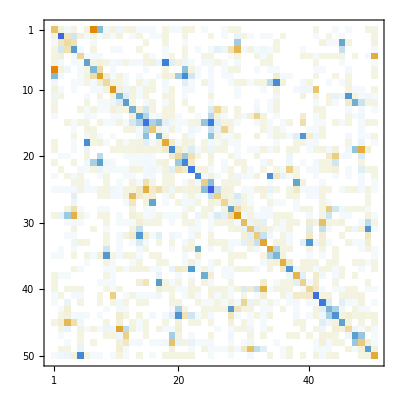
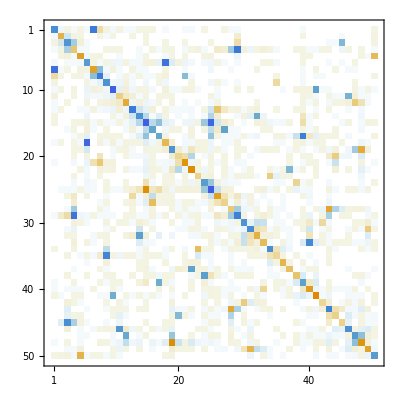
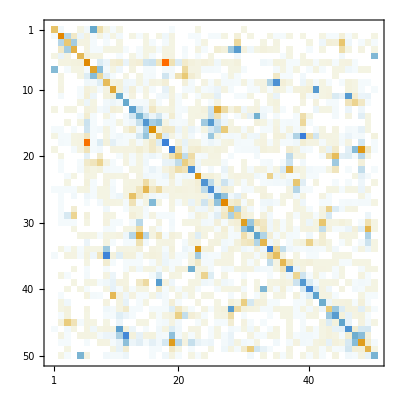
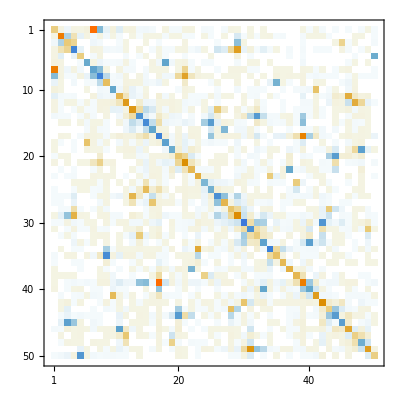
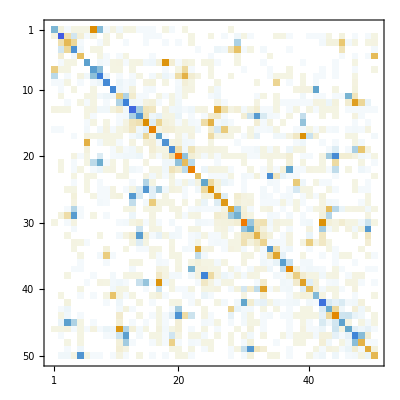

```mathematica
Plots3D2=Table[ListPlot3D[(Transpose[BigOs⟦1⟧]).M⟦i⟧.BigOs⟦3⟧,PlotRange->All],{i,nPCA}];
PlotsMatrices2=Table[MatrixPlot[(Transpose[BigOs⟦1⟧]).M⟦i⟧.BigOs⟦3⟧,PlotRange->All],{i,nPCA}]
```

```mathematica
(*Plots3D2⟦1⟧
Plots3D2⟦2⟧
Plots3D2⟦3⟧
Plots3D2⟦4⟧
Plots3D2⟦5⟧
Plots3D2⟦6⟧*)
```

```mathematica
(*
M⟦1⟧⟦1,All⟧//ListLinePlot[#,PlotRange->All]&
M⟦2⟧⟦1,All⟧//ListLinePlot[#,PlotRange->All]&
M⟦3⟧⟦1,All⟧//ListLinePlot[#,PlotRange->All]&
M⟦4⟧⟦1,All⟧//ListLinePlot[#,PlotRange->All]&
M⟦5⟧⟦1,All⟧//ListLinePlot[#,PlotRange->All]&
*)
```

```mathematica
(*
MatrixPlot[EigenCov[[2,2]]]
*)
```

```mathematica
(*
EigenCov[[2,1]]//DiagonalMatrix//MatrixPlot
*)
```

```mathematica
(*
Plot[p[l],{l,0,nn}]
*)
```

```mathematica
Table[ListLinePlot[Diagonal[(Transpose[BigOs⟦1⟧]).M⟦i⟧.BigOs⟦3⟧],PlotRange->All],{i,nPCA}];
```

#### Model

```mathematica
meanMat=Table[RotateRight[Take[Mean[Data],ll],j-1],{j,1,ll}]+Table[RotateLeft[Take[Mean[Data],-ll],j-1],{j,1,ll}];
```

```mathematica
Mat=(meanMat+If[Re[EigenCov⟦2,1,1⟧]>0,RandomVariate[NormalDistribution[0,Re[EigenCov⟦2,1,1⟧]]],0] M⟦1⟧+If[Re[EigenCov⟦2,1,2⟧]>0,RandomVariate[NormalDistribution[0,Re[EigenCov⟦2,1,2⟧]]],0] M⟦2⟧)//Re;
Matt=(meanMat+Sum[If[Re[EigenCov⟦2,1,i⟧]>0,RandomVariate[NormalDistribution[0,Re[EigenCov⟦2,1,i⟧]]],0] M⟦i⟧,{i,1,nPCA}])//Re;
```

-Graphics3D-

-Graphics3D-

-Graphics3D-

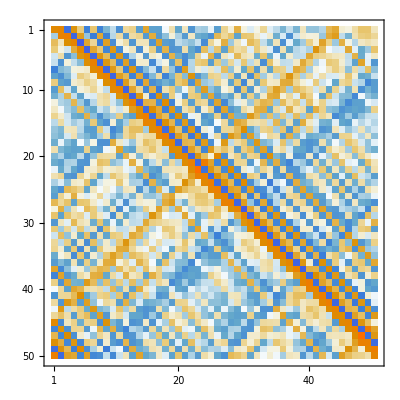

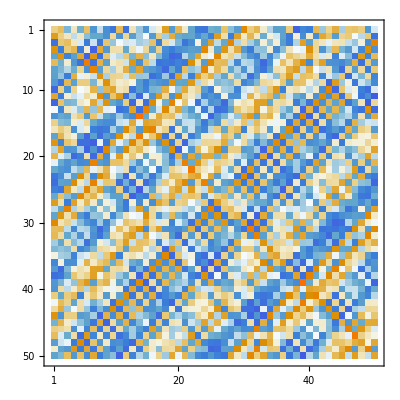

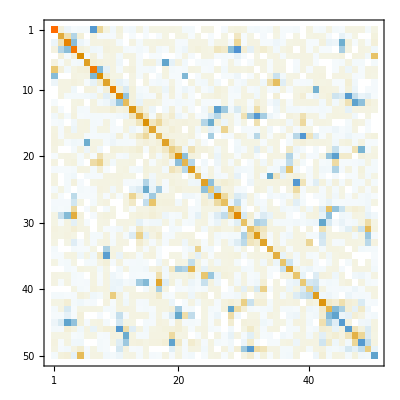

```mathematica
ListPlot3D[Mat,PlotRange->All]
ListPlot3D[Matt,PlotRange->All]
ListPlot3D[(Transpose[BigOs⟦1⟧]).Mat.BigOs⟦3⟧,PlotRange->All]
MatrixPlot[Mat,PlotRange->All]
MatrixPlot[Matt,PlotRange->All]
MatrixPlot[(Transpose[BigOs⟦1⟧]).Mat.BigOs⟦3⟧,PlotRange->All]
```

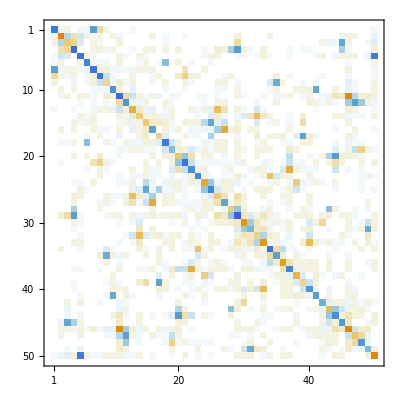
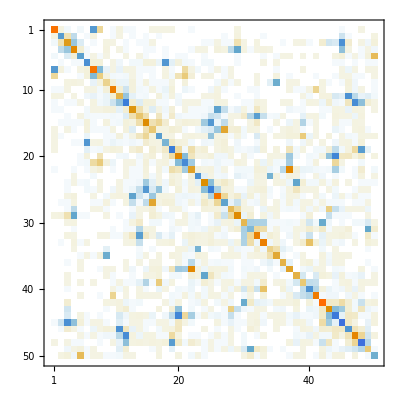
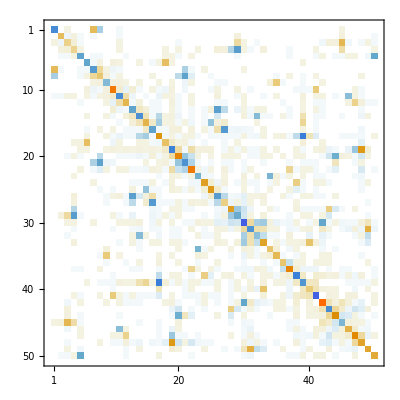
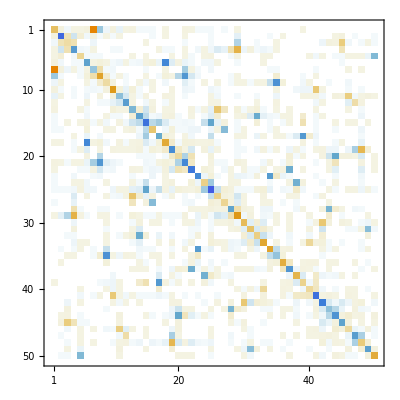
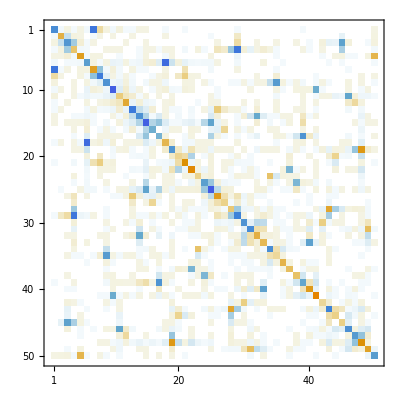
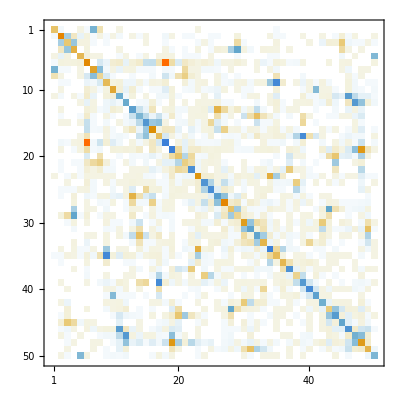

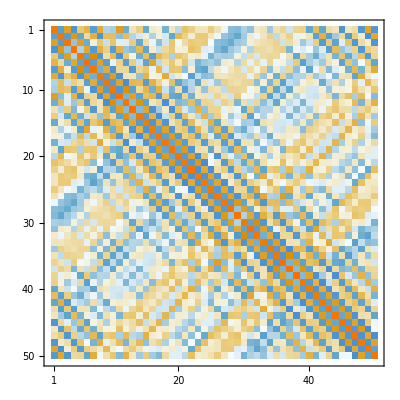
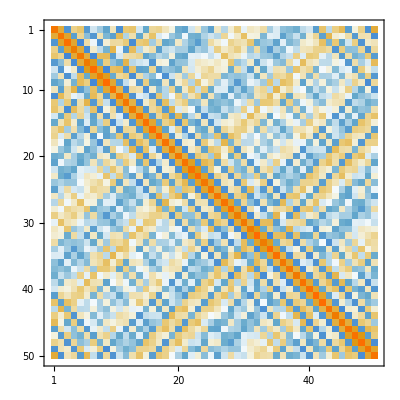

```mathematica
PlotsMatrices2=Table[MatrixPlot[(Transpose[BigOs⟦1⟧]).M⟦i⟧.BigOs⟦3⟧+(((Transpose[BigOs⟦1⟧]).M⟦i⟧.BigOs⟦3⟧)//Transpose),PlotRange->All],{i,1,6}]
PlotsMatrices2=Table[MatrixPlot[M⟦i⟧+(M⟦i⟧//Transpose),PlotRange->All],{i,1,6}]
```